```mathematica
g = 9.81;
l = 1;
```

5.10841

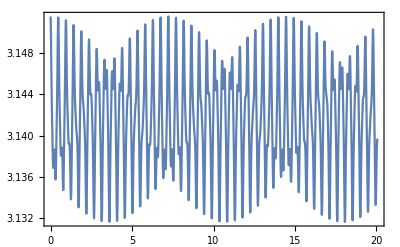

```mathematica
A=0.4;Ω=40;initpos=π+0.01;
ω0=Sqrt[g/l];(A Ω)/(l ω0)
sol=NDSolve[{θ''[t] +(g/l-(A Ω^2/l) Cos[Ω t])Sin[θ[t]]==0, θ[0]==initpos, θ'[0] == 0}, θ[t], {t,0, 100*π*Sqrt[l/g] }];
Plot[θ[t]/.sol[[1]],{t,0, 20*π*Sqrt[l/g]},Frame->True,PlotRange->All]
```

```mathematica
α=ω0^2/Ω^2
```

0.0109

```mathematica
ω0
```

3.13209

```mathematica
Animate[Graphics[{EdgeForm[Thick],White,Rectangle[{-1.65,-1.65},{1.65,1.65}],Black,Disk[{0,A Cos[Ω s]},0.01],Line[{{0,A Cos[Ω s]},{l Sin[θ[t]]/.sol[[1]]/.t->s,A Cos[Ω s]- l Cos[θ[t]]/.sol[[1]]/.t->s}}],Disk[{l Sin[θ[t]]/.sol[[1]]/.t->s,A Cos[Ω s]- l Cos[θ[t]]/.sol[[1]]/.t->s},0.02]}],{s,0, 20*π*Sqrt[l/g],20*π*Sqrt[l/g]/10000},AnimationRate->0.5]
```